## Disordered resetting

### We already know the functional form of the MFTP (F1) and the second moment (F2) in function of the probability of the target position (p if +xt or (1-p) if -xt).

```mathematica
F1Plus[x_,y_]:=1/x^2(Cosh[x]+x/y Sinh[x]-1);
F1Minus[x_,y_]:=F1Plus[y,x];
F1Total[x_,y_,p_]:=p F1Plus[x,y]+(1-p)F1Minus[x,y];
F2Plus[x_,y_]:=
1/(y^3 x^4)((y^2-x^2)y+(x^2-y^2(y+3))x Sinh[x]+(y^2+x^2)y Cosh[2x]-(x^2+2y-4x Sinh[x])y^2 Cosh[x]);
F2Minus[x_,y_]:=F2Plus[y,x];
F2Total[x_,y_,p_]:=p F2Plus[x,y]+(1-p)F2Minus[x,y];
```

## Density plots (Figure 3)

```mathematica
<<MaTeX`
LTicks[xm_,xM_,ΔxM_,Δxm_]:=Join[Table[{x,NumberForm[x,{1,1}],{0.02,0},Thickness[0.004]},{x,xm,xM,ΔxM}],Table[{x,"",{0.01,0},Thickness[0.002]},{x,xm,xM,Δxm}]];

STicks[xm_,xM_,ΔxM_,Δxm_]:=Join[Table[{x,"",{0.02,0},Thickness[0.004]},{x,xm,xM,ΔxM}],Table[{x,"",{0.01,0},Thickness[0.002]},{x,xm,xM,Δxm}]];
```

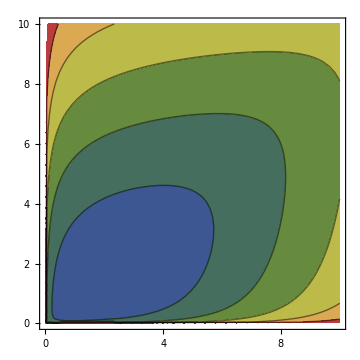

```mathematica
xm=0;xM=10;Δxm=1;ΔxM=2;max=4;nc=5;step=0.8;
ContourPlot[Log10[F1Total[g1,g2,0.25]],{g1,0,10},{g2,0,10},PlotRange->{{0,10},{0,10},{0,max}},ColorFunction->ColorData["DarkRainbow"],Contours->nc,PlotLegends->BarLegend[{"DarkRainbow",{0,max}},Subdivide[max,nc],Ticks->Table[{Round[x,10^-1],NumberForm[N[Round[x,10^-1]],{2,1}]},{x,0,max,step}],LegendMarkerSize->250,LegendLabel->MaTeX["\\tau",Magnification->2],LegendMargins->{{-4,0},{35,0}}],LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],RotateLabel->False,Axes->False,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameLabel->{MaTeX["\\gamma_1",Magnification->2],MaTeX["\\gamma_2",Magnification->2]},ImageSize->Medium,FrameTicks->{{LTicks[xm,xM,ΔxM,Δxm],STicks[xm,xM,ΔxM,Δxm]},{LTicks[xm,xM,ΔxM,Δxm],STicks[xm,xM,ΔxM,Δxm]}},PlotRangeClipping->False]
```

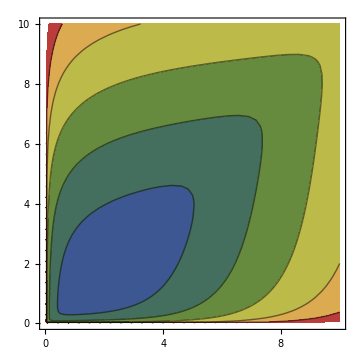

```mathematica
xm=0;xM=10;Δxm=1;ΔxM=2;max=4;step=0.8;nc=5;
ContourPlot[Log10[Sqrt[STDTotal[g1,g2,0.25]]],{g1,0,10},{g2,0,10},PlotRange->{{0,10},{0,10},{0,max}},ColorFunction->ColorData["DarkRainbow"],Contours->nc,PlotLegends->BarLegend[{"DarkRainbow",{0,max}},Subdivide[max,nc],Ticks->Table[{Round[x,10^-1],NumberForm[N[Round[x,10^-1]],{2,1}]},{x,0,max,step}],LegendMarkerSize->250,LegendLabel->MaTeX["\\sigma",Magnification->2],LegendMargins->{{-4,0},{35,0}}],LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],RotateLabel->False,Axes->False,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameLabel->{MaTeX["\\gamma_1",Magnification->2],MaTeX["\\gamma_2",Magnification->2]},ImageSize->Medium,FrameTicks->{{LTicks[xm,xM,ΔxM,Δxm],STicks[xm,xM,ΔxM,Δxm]},{LTicks[xm,xM,ΔxM,Δxm],STicks[xm,xM,ΔxM,Δxm]}},PlotRangeClipping->False]
```

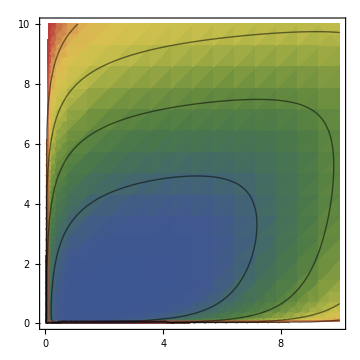

```mathematica
p=0.1;xm=0;xM=10;Δxm=1;ΔxM=2;max=4;nc=7;step=1;
Show[DensityPlot[Log10[F1Total[g1,g2,p]],{g1,xm,xM},{g2,xm,xM},PlotRange->{{xm,xM},{xm,xM},{0,max}},ColorFunction->ColorData["DarkRainbow"],PlotLegends->BarLegend[{"DarkRainbow",{0,max}},Ticks->Table[{Round[x,10^-2],NumberForm[N[Round[x,10^-2]],{3,2}]},{x,0,max,step}],LegendMarkerSize->250,LegendLabel->MaTeX["\\log_{10} \\tau",Magnification->2],LegendMargins->{{-4,0},{35,0}}],LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],RotateLabel->False,Axes->False,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameLabel->{MaTeX["\\gamma_1",Magnification->2],MaTeX["\\gamma_2",Magnification->2]},ImageSize->Medium,FrameTicks->{{LTicks[xm,xM,ΔxM,Δxm],STicks[xm,xM,ΔxM,Δxm]},{LTicks[xm,xM,ΔxM,Δxm],STicks[xm,xM,ΔxM,Δxm]}},PlotRangeClipping->False],ContourPlot[Log10[F1Total[g1,g2,p]],{g1,xm,xM},{g2,xm,xM},Contours->max/step,ContourShading->False]]
```

### Densityplot p=0

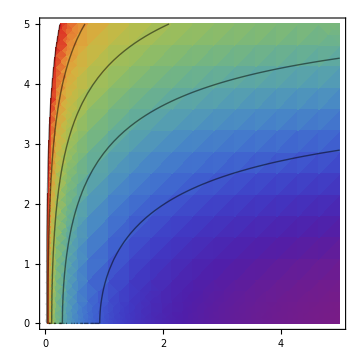

```mathematica
p=0;xm=0;xM=5;Δxm=0.5;ΔxM=1;ym=0;yM=5;Δym=0.5;ΔyM=1;min=-0.2;max=1.8;step=0.4;Colors="Rainbow";
MFTPp0=Show[DensityPlot[Log10[F1Total[g1,g2,p]],{g1,xm,xM},{g2,ym,yM},PlotRange->{{xm,xM},{ym,yM},{min,max}},ColorFunction->ColorData[Colors],PlotLegends->BarLegend[{Colors,{min,max}},Ticks->Table[{Round[x,10^-2],NumberForm[N[Round[x,10^-2]],{3,1}]},{x,min,max,step}],LegendMarkerSize->250,LegendLabel->MaTeX["\\log_{10} \\tau^{(1)}",Magnification->2],LegendMargins->{{-4,0},{35,0}}],LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],RotateLabel->False,Axes->False,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameLabel->{MaTeX["\\alpha_+",Magnification->2],MaTeX["\\alpha_-",Magnification->2]},ImageSize->Medium,FrameTicks->{{LTicks[ym,yM,ΔyM,Δym],STicks[ym,yM,ΔyM,Δym]},{LTicks[xm,xM,ΔxM,Δxm],STicks[xm,xM,ΔxM,Δxm]}},PlotRangeClipping->False],ContourPlot[Log10[F1Total[g1,g2,p]],{g1,xm,xM},{g2,ym,yM},PlotRange->{{xm,xM},{ym,yM},{min,max}},Contours->Table[x-0.00001,{x,min,max,step}],ContourShading->False]]
```

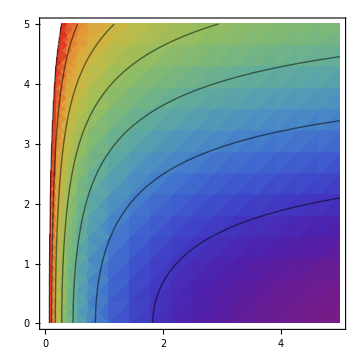

```mathematica
p=0;xm=0;xM=5;Δxm=0.5;ΔxM=1;ym=0;yM=5;Δym=0.5;ΔyM=1;min=-0.3;max=1.8;step=0.3;Colors="Rainbow";
STDp0=Show[DensityPlot[Log10[F2Total[g1,g2,p]-F1Total[g1,g2,p]^2]/2,{g1,xm,xM},{g2,ym+0.01,yM},PlotRange->{{xm,xM},{ym,yM},{min,max}},ColorFunction->ColorData[Colors],PlotLegends->BarLegend[{Colors,{min,max}},Ticks->Table[{Round[x,10^-2],NumberForm[N[Round[x,10^-2]],{3,1}]},{x,min,max,step}],LegendMarkerSize->250,LegendLabel->MaTeX["\\log_{10} \\sigma_\\tau",Magnification->2],LegendMargins->{{-4,0},{35,0}}],LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],RotateLabel->False,Axes->False,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameLabel->{MaTeX["\\alpha_+",Magnification->2],MaTeX["\\alpha_-",Magnification->2]},ImageSize->Medium,FrameTicks->{{LTicks[ym,yM,ΔyM,Δym],STicks[ym,yM,ΔyM,Δym]},{LTicks[xm,xM,ΔxM,Δxm],STicks[xm,xM,ΔxM,Δxm]}},PlotRangeClipping->False],ContourPlot[Log10[STDTotal[g1,g2,p]]/2,{g1,xm,xM},{g2,ym+0.01,yM},PlotRange->{{xm,xM},{ym,yM},{min,max}},Contours->Table[x-0.00001,{x,min,max,step}],ContourShading->False]]
```

```mathematica
Export["/Users/gregarval/Documents/DensityPlot_MFTP_p=0.png",MFTPp0,ImageResolution->600]
```

/Users/gregarval/Documents/DensityPlot_MFTP_p=0.png

```mathematica
Export["/Users/gregarval/Documents/DensityPlot_STD_p=0.png",STDp0,ImageResolution->600]
```

/Users/gregarval/Documents/DensityPlot_STD_p=0.png

### Densityplot p=0.05

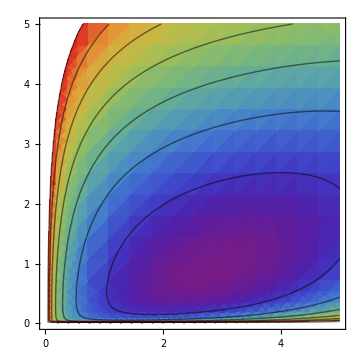

```mathematica
p=0.05;xm=0;xM=5;Δxm=0.5;ΔxM=1;ym=0;yM=5;Δym=0.5;ΔyM=1;max=1.4;step=0.2;Colors="Rainbow";
MFTPp005=Show[DensityPlot[Log10[F1Total[g1,g2,p]],{g1,xm,xM},{g2,ym,yM},PlotRange->{{xm,xM},{ym,yM},{0,max}},ColorFunction->ColorData[Colors],PlotLegends->BarLegend[{Colors,{0,max}},Ticks->Table[{Round[x,10^-2],NumberForm[N[Round[x,10^-2]],{3,1}]},{x,0,max,step}],LegendMarkerSize->250,LegendLabel->MaTeX["\\log_{10} \\tau^{(1)}",Magnification->2],LegendMargins->{{-4,0},{35,0}}],LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],RotateLabel->False,Axes->False,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameLabel->{MaTeX["\\alpha_+",Magnification->2],MaTeX["\\alpha_-",Magnification->2]},ImageSize->Medium,FrameTicks->{{LTicks[ym,yM,ΔyM,Δym],STicks[ym,yM,ΔyM,Δym]},{LTicks[xm,xM,ΔxM,Δxm],STicks[xm,xM,ΔxM,Δxm]}},PlotRangeClipping->False],ContourPlot[Log10[F1Total[g1,g2,p]],{g1,xm,xM},{g2,ym,yM},PlotRange->{{xm,xM},{ym,yM},{0,max}},Contours->Table[x-0.00001,{x,0,max,step}],ContourShading->False]]
```

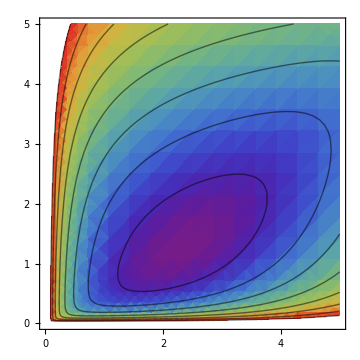

```mathematica
p=0.05;xm=0;xM=5;Δxm=0.5;ΔxM=1;ym=0;yM=xM;Δym=0.5;ΔyM=1;max=1.6;step=0.2;Colors="Rainbow";
STDp005=Show[DensityPlot[Log10[F2Total[g1,g2,0.05]-F1Total[g1,g2,0.05]^2]/2,{g1,xm,xM},{g2,ym,yM},PlotRange->{{xm,xM},{ym,yM},{0,max}},ColorFunction->ColorData[Colors],PlotLegends->BarLegend[{Colors,{0,max}},Ticks->Table[{Round[x,10^-2],NumberForm[N[Round[x,10^-2]],{3,1}]},{x,0,max,step}],LegendMarkerSize->250,LegendLabel->MaTeX["\\log_{10} \\sigma_\\tau",Magnification->2],LegendMargins->{{-4,0},{35,0}}],LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],RotateLabel->False,Axes->False,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameLabel->{MaTeX["\\alpha_+",Magnification->2],MaTeX["\\alpha_-",Magnification->2]},ImageSize->Medium,FrameTicks->{{LTicks[ym,yM,ΔyM,Δym],STicks[ym,yM,ΔyM,Δym]},{LTicks[xm,xM,ΔxM,Δxm],STicks[xm,xM,ΔxM,Δxm]}},PlotRangeClipping->False],ContourPlot[Log10[F2Total[g1,g2,0.05]-F1Total[g1,g2,0.05]^2]/2,{g1,xm,xM},{g2,ym,yM},PlotRange->{{xm,xM},{ym,yM},{0,max}},Contours->Table[x-0.00001,{x,0,max,step}],ContourShading->False]]
```

```mathematica
Export["/Users/gregarval/Documents/DensityPlot_MFTP_p=0_05.png",MFTPp005,ImageResolution->600]
```

/Users/gregarval/Documents/DensityPlot_MFTP_p=0_05.png

```mathematica
Export["/Users/gregarval/Documents/DensityPlot_STD_p=0_05.png",STDp005,ImageResolution->600]
```

/Users/gregarval/Documents/DensityPlot_STD_p=0_05.png

### Densityplot p=0.3

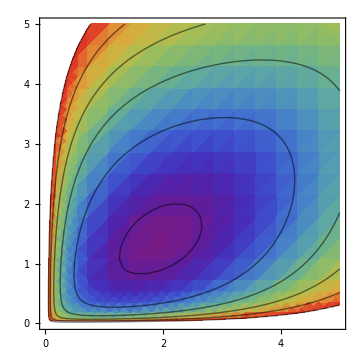

```mathematica
p=0.3;xm=0;xM=5;Δxm=0.5;ΔxM=1;ym=0;yM=5;Δym=0.5;ΔyM=1;max=1.2;step=0.2;Colors="Rainbow";
MFTP03=Show[DensityPlot[Log10[F1Total[g1,g2,p]],{g1,xm,xM},{g2,ym,yM},PlotRange->{{xm,xM},{ym,yM},{0,max}},ColorFunction->ColorData[Colors],PlotLegends->BarLegend[{Colors,{0,max}},Ticks->Table[{Round[x,10^-2],NumberForm[N[Round[x,10^-2]],{3,1}]},{x,0,max,step}],LegendMarkerSize->250,LegendLabel->MaTeX["\\log_{10} \\tau^{(1)}",Magnification->2],LegendMargins->{{-4,0},{35,0}}],LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],RotateLabel->False,Axes->False,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameLabel->{MaTeX["\\alpha_+",Magnification->2],MaTeX["\\alpha_-",Magnification->2]},ImageSize->Medium,FrameTicks->{{LTicks[ym,yM,ΔyM,Δym],STicks[ym,yM,ΔyM,Δym]},{LTicks[xm,xM,ΔxM,Δxm],STicks[xm,xM,ΔxM,Δxm]}},PlotRangeClipping->False],ContourPlot[Log10[F1Total[g1,g2,p]],{g1,xm,xM},{g2,ym,yM},PlotRange->{{xm,xM},{ym,yM},{0,max}},Contours->Table[x-0.00001,{x,0,max,step}],ContourShading->False]]
```

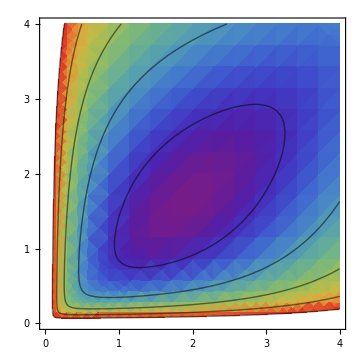

```mathematica
p=0.3;xm=0;xM=4;Δxm=0.5;ΔxM=1;ym=0;yM=xM;Δym=0.5;ΔyM=1;max=1.5;step=0.3;Colors="Rainbow";
STD03=Show[DensityPlot[Log10[F2Total[g1,g2,p]-F1Total[g1,g2,p]^2]/2,{g1,xm,xM},{g2,ym,yM},PlotRange->{{xm,xM},{ym,yM},{0,max}},ColorFunction->ColorData[Colors],PlotLegends->BarLegend[{Colors,{0,max}},Ticks->Table[{Round[x,10^-2],NumberForm[N[Round[x,10^-2]],{3,1}]},{x,0,max,step}],LegendMarkerSize->250,LegendLabel->MaTeX["\\log_{10} \\sigma_\\tau",Magnification->2],LegendMargins->{{-4,0},{35,0}}],LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],RotateLabel->False,Axes->False,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameLabel->{MaTeX["\\alpha_+",Magnification->2],MaTeX["\\alpha_-",Magnification->2]},ImageSize->Medium,FrameTicks->{{LTicks[ym,yM,ΔyM,Δym],STicks[ym,yM,ΔyM,Δym]},{LTicks[xm,xM,ΔxM,Δxm],STicks[xm,xM,ΔxM,Δxm]}},PlotRangeClipping->False],ContourPlot[Log10[STDTotal[g1,g2,p]]/2,{g1,xm,xM},{g2,ym,yM},PlotRange->{{xm,xM},{ym,yM},{0,max}},Contours->Table[x-0.00001,{x,0,max,step}],ContourShading->False]]
```

```mathematica
Export["/Users/gregarval/Documents/DensityPlot_MFTP_p=0_3.png",MFTP03,ImageResolution->600]
```

/Users/gregarval/Documents/DensityPlot_MFTP_p=0_3.png

```mathematica
Export["/Users/gregarval/Documents/DensityPlot_STD_p=0_3.png",STD03,ImageResolution->600]
```

/Users/gregarval/Documents/DensityPlot_STD_p=0_3.png

### Densityplot p=0.5

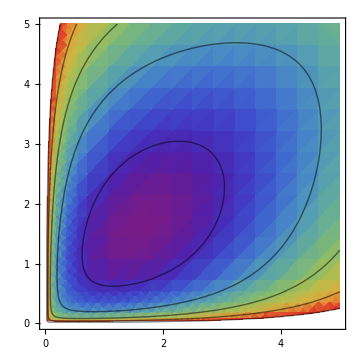

```mathematica
p=0.5;xm=0;xM=5;Δxm=0.5;ΔxM=1;ym=0;yM=xM;Δym=0.5;ΔyM=1;max=1.5;step=0.3;Colors="Rainbow";
MFTPp05=Show[DensityPlot[Log10[F1Total[g1,g2,p]],{g1,xm,xM},{g2,ym,yM},PlotRange->{{xm,xM},{ym,yM},{0,max}},ColorFunction->ColorData[Colors],PlotLegends->BarLegend[{Colors,{0,max}},Ticks->Table[{Round[x,10^-2],NumberForm[N[Round[x,10^-2]],{3,1}]},{x,0,max,step}],LegendMarkerSize->250,LegendLabel->MaTeX["\\log_{10} \\tau^{(1)}",Magnification->2],LegendMargins->{{-4,0},{35,0}}],LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],RotateLabel->False,Axes->False,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameLabel->{MaTeX["\\alpha_+",Magnification->2],MaTeX["\\alpha_-",Magnification->2]},ImageSize->Medium,FrameTicks->{{LTicks[ym,yM,ΔyM,Δym],STicks[ym,yM,ΔyM,Δym]},{LTicks[xm,xM,ΔxM,Δxm],STicks[xm,xM,ΔxM,Δxm]}},PlotRangeClipping->False],ContourPlot[Log10[F1Total[g1,g2,p]],{g1,xm,xM},{g2,ym,yM},PlotRange->{{xm,xM},{ym,yM},{0,max}},Contours->Table[x-0.00001,{x,0,max,step}],ContourShading->False]]
```

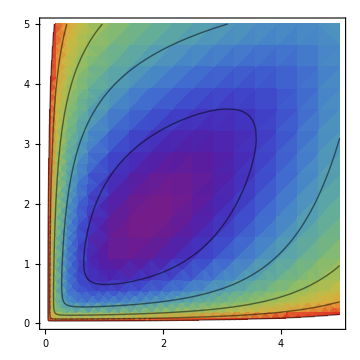

```mathematica
p=0.5;xm=0;xM=5;Δxm=0.5;ΔxM=1;ym=0;yM=xM;Δym=0.5;ΔyM=1;max=2;step=0.4;Colors="Rainbow";
STDp05=Show[DensityPlot[Log10[F2Total[g1,g2,p]-F1Total[g1,g2,p]^2]/2,{g1,xm,xM},{g2,ym,yM},PlotRange->{{xm,xM},{ym,yM},{0,max}},ColorFunction->ColorData[Colors],PlotLegends->BarLegend[{Colors,{0,max}},Ticks->Table[{Round[x,10^-2],NumberForm[N[Round[x,10^-2]],{3,1}]},{x,0,max,step}],LegendMarkerSize->250,LegendLabel->MaTeX["\\log_{10} \\sigma_\\tau",Magnification->2],LegendMargins->{{-4,0},{35,0}}],LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],RotateLabel->False,Axes->False,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameLabel->{MaTeX["\\alpha_+",Magnification->2],MaTeX["\\alpha_-",Magnification->2]},ImageSize->Medium,FrameTicks->{{LTicks[ym,yM,ΔyM,Δym],STicks[ym,yM,ΔyM,Δym]},{LTicks[xm,xM,ΔxM,Δxm],STicks[xm,xM,ΔxM,Δxm]}},PlotRangeClipping->False],ContourPlot[Log10[F2Total[g1,g2,p]-F1Total[g1,g2,p]^2]/2,{g1,xm,xM},{g2,ym,yM},PlotRange->{{xm,xM},{ym,yM},{0,max}},Contours->Table[x-0.00001,{x,0,max,step}],ContourShading->False]]
```

```mathematica
Export["/Users/gregarval/Documents/DensityPlot_MFTP_p=0_5.png",MFTPp05,ImageResolution->600]
```

/Users/gregarval/Documents/DensityPlot_MFTP_p=0_5.png

```mathematica
Export["/Users/gregarval/Documents/DensityPlot_STD_p=0_5.png",STDp05,ImageResolution->600]
```

/Users/gregarval/Documents/DensityPlot_STD_p=0_5.png

## Simulations of MFTP and STD (Figure 2)

```mathematica
(*For[i=1,i<=10,i++,Evaluate[Symbol["p0"<>ToString[i]]]={}]*)
```

```mathematica
Clear["Global`*"]
```

```mathematica
folder="0"; 
mean={};var={};Filevar={};
SetDirectory["/Users/gregarval/projects/Disordered resetting/Results_Paper/Mapping_r1/p=" <>folder];
files=FileNames["*.dat"];
For[i=1,i<=Length[files],i++,
Filevar=Import[TextString["Results_" <> ToString[i]<>".dat"]][[1]];
AppendTo[mean, Mean[Filevar]]  ;
AppendTo[var, Mean[Filevar^2]] ;
]; 
Evaluate[Symbol["mean0"<>StringTake[folder,-1]]]=mean; 
Evaluate[Symbol["var0"<>StringTake[folder,-1]]]=var;
```

```mathematica
folder="0,50"; (*Use for "0,05", "0,30" and "0,50"*)
mean={};var={};Filevar={};
SetDirectory["/Users/gregarval/projects/Disordered resetting/Results_Paper/Mapping_r1/p=" <>folder];
files=FileNames["*.dat"];
(*For[i=1,i<=Length[files],i++, AppendTo[var,Mean[Import[TextString[files[[i]]]][[1]]]]];*) 
For[i=1,i<=Length[files],i++,  

Filevar=Import[TextString["Results_" <> ToString[i]<>".dat"]][[1]];AppendTo[mean, Mean[Filevar]]  ;
AppendTo[var, Mean[Filevar^2]] ;
]; 
Evaluate[Symbol["mean0"<>StringTake[folder,-2]]]=mean; 
Evaluate[Symbol["var0"<>StringTake[folder,-2]]]=var;
```

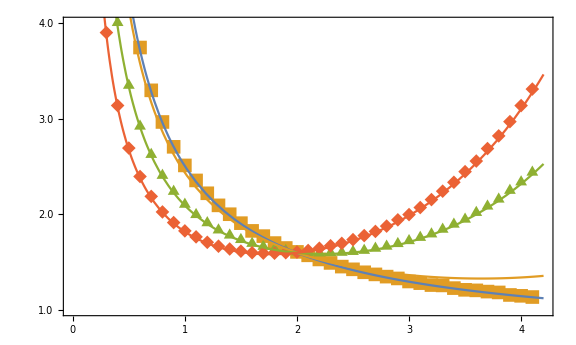

```mathematica
xm=0;xM=4.4;Δxm=0.5;ΔxM=1;ym=0;yM=4;Δym=0.25;ΔyM=0.5;SizeLegend=1.5;SizeDots=12;tauPaper=Show[ListPlot[{Transpose@{Range[0.2,4.1,0.1],mean00},Transpose@{Range[0.2,4.1,0.1],mean005},Transpose@{Range[0.2,4.1,0.1],mean030},Transpose@{Range[0.2,4.1,0.1],mean050}},PlotMarkers->{Style["●",Thick,SizeDots],Style["■",Thick,SizeDots+2],Style["▲",Thick,SizeDots+2],Style["◆",Thick,SizeDots+2]},PlotLegends->Placed[{MaTeX["p = 0",Magnification->SizeLegend],MaTeX["p = 0.05",Magnification->SizeLegend],MaTeX["p = 0.3",Magnification->SizeLegend],MaTeX["p = 0.5",Magnification->SizeLegend]},{0.6,0.7}]],Plot[{F1Total[g1,2,0],F1Total[g1,2,0.05],F1Total[g1,2,0.30],F1Total[g1,2,0.50]},{g1,0.1,4.2},PlotRange->All],Frame-> True,FrameLabel->{MaTeX["\\alpha_+",Magnification->2],MaTeX["\\tau^{(1)}",Magnification->2]},PlotRange->{{0,4.2},{1,4}},Axes-> False,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameTicks->{{LTicks[ym,yM,ΔyM,Δym],STicks[ym,yM,ΔyM,Δym]},{LTicks[xm,xM,ΔxM,Δxm],STicks[xm,xM,ΔxM,Δxm]}},ImageSize->Large,AspectRatio->0.6,PlotRangePadding->None,ImagePadding->{{70,5},{60,10}}]
```

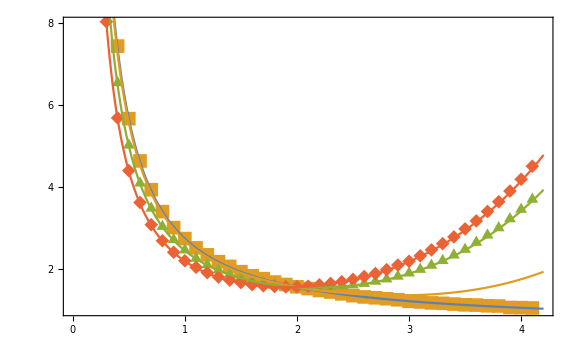

```mathematica
xm=0;xM=4.4;Δxm=0.5;ΔxM=1;ym=0;yM=8;Δym=0.5;ΔyM=1;SizeLegend=1.5;sigmaPaper=Show[ListPlot[{Transpose@{Range[0.2,4.1,0.1],Sqrt[var00-mean00^2]},Transpose@{Range[0.2,4.1,0.1],Sqrt[var005-mean005^2]},Transpose@{Range[0.2,4.1,0.1],Sqrt[var030-mean030^2]},Transpose@{Range[0.2,4.1,0.1],Sqrt[var050-mean050^2]}},PlotMarkers->{Style["●",Thick,SizeDots],Style["■",Thick,SizeDots+2],Style["▲",Thick,SizeDots+2],Style["◆",Thick,SizeDots+2]},PlotLegends->Placed[{MaTeX["p = 0",Magnification->SizeLegend],MaTeX["p = 0.05",Magnification->SizeLegend],MaTeX["p = 0.3",Magnification->SizeLegend],MaTeX["p = 0.5",Magnification->SizeLegend]},{0.6,0.7}]],Plot[{Sqrt[F2Total[g1,2,0.]-F1Total[g1,2,0]^2],Sqrt[F2Total[g1,2,0.05]-F1Total[g1,2,0.05]^2],Sqrt[F2Total[g1,2,0.3]-F1Total[g1,2,0.3]^2],Sqrt[F2Total[g1,2,0.5]-F1Total[g1,2,0.5]^2]},{g1,0.1,4.2},PlotRange->All],Frame-> True,FrameLabel->{MaTeX["\\alpha_+",Magnification->2],MaTeX["\\sigma_\\tau",Magnification->2]},PlotRange->{{0,4.2},{1,8}},Axes-> False,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameTicks->{{LTicks[ym,yM,ΔyM,Δym],STicks[ym,yM,ΔyM,Δym]},{LTicks[xm,xM,ΔxM,Δxm],STicks[xm,xM,ΔxM,Δxm]}},ImageSize->Large,AspectRatio->0.6,PlotRangePadding->None,ImagePadding->{{70,5},{60,10}}]
```

```mathematica
Export["/Users/gregarval/Documents/MFTP_Disordered.png",tauPaper,ImageResolution->1200]
```

/Users/gregarval/Documents/MFTP_Disordered.png

```mathematica
Export["/Users/gregarval/Documents/StandardDeviation_Disordered.png",sigmaPaper,ImageResolution->1200]
```

/Users/gregarval/Documents/StandardDeviation_Disordered.png